# Phase Portrait

### Author

Eric W. Weisstein
February 28, 2011

This notebook downloaded from http://mathworld.wolfram.com/notebooks/DifferentialEquations/PhasePortrait.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/PhasePortrait.html.

©2011 Wolfram Research, Inc. except for portions noted otherwise

## Plots

#### V5

```mathematica
<<Graphics`Colors`
<<Typesetting`
```

```mathematica
Show[GraphicsArray[
{
ParametricPlot[Evaluate[Table[{x[t],y[t]}/.DSolve[{x'[t]==y[t],y'[t]==-10 x[t],x[0]==c,y[0]==0},{x[t],y[t]},t][[1]],{c,10}]],{t,0,2},PlotRange->All,PlotStyle->Red,
DisplayFunction->Identity,
AxesLabel->TraditionalForm/@{x,""},PlotLabel->StyleForm["simple harmonic oscillator",FontFamily->"Times",FontSlant->"Italic"]],
ParametricPlot[
Evaluate[Join[{x[t],y[t]}/.NDSolve[{x'[t]==y[t],y'[t]==-.26Sin[x[t]],x[0]==0,y[0]==#},{x[t],y[t]},{t,-30,30}][[1]]&/@{-3.5,-3,-2,-1.7,Sequence@@Range[-1.5,-1,.2],-1.02,Sequence@@Range[0,1.5,.2],1.02,1.7,2,3,3.5},
{x[t],y[t]}/.NDSolve[{x'[t]==y[t],y'[t]==-.26Sin[x[t]],x[0]==-2Pi,y[0]==#},{x[t],y[t]},{t,-30,30}][[1]]&/@Range[0,1,.2],
{x[t],y[t]}/.NDSolve[{x'[t]==y[t],y'[t]==-.26Sin[x[t]],x[0]==2Pi,y[0]==#},{x[t],y[t]},{t,-30,30}][[1]]&/@Range[0,1,.2]
]],{t,-20,20},PlotRange->{{-5,5},{-2,2}},PlotStyle->Red,
DisplayFunction->Identity,
AxesLabel->TraditionalForm/@{x,""},PlotLabel->StyleForm["pendulum",FontFamily->"Times",FontSlant->"Italic"]]
}]]
```

⁃GraphicsArray⁃

#### V6

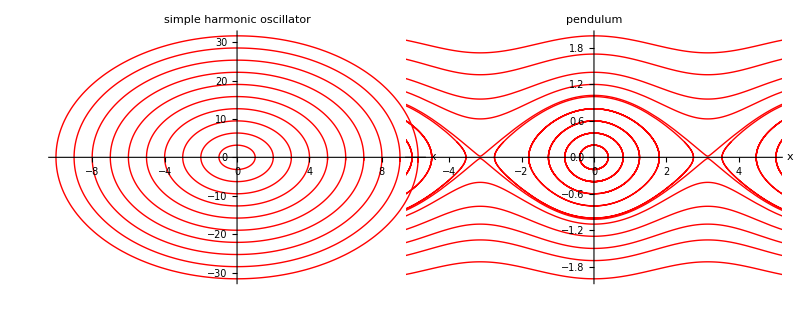

```mathematica
GraphicsRow[
{
ParametricPlot[Evaluate[Table[{x[t],y[t]}/.DSolve[{x'[t]==y[t],y'[t]==-10 x[t],x[0]==c,y[0]==0},{x[t],y[t]},t][[1]],{c,10}]],{t,0,2},PlotRange->All,PlotStyle->Red,
AspectRatio->.7,
AxesLabel->{x,""},PlotLabel->TextCell[Style["simple harmonic oscillator",Italic],PageWidth->120,TextAlignment->Center]],
ParametricPlot[
Evaluate[Join[{x[t],y[t]}/.NDSolve[{x'[t]==y[t],y'[t]==-.26Sin[x[t]],x[0]==0,y[0]==#},{x[t],y[t]},{t,-30,30}][[1]]&/@{-3.5,-3,-2,-1.7,Sequence@@Range[-1.5,-1,.2],-1.02,Sequence@@Range[0,1.5,.2],1.02,1.7,2,3,3.5},
{x[t],y[t]}/.NDSolve[{x'[t]==y[t],y'[t]==-.26Sin[x[t]],x[0]==-2Pi,y[0]==#},{x[t],y[t]},{t,-30,30}][[1]]&/@Range[0,1,.2],
{x[t],y[t]}/.NDSolve[{x'[t]==y[t],y'[t]==-.26Sin[x[t]],x[0]==2Pi,y[0]==#},{x[t],y[t]},{t,-30,30}][[1]]&/@Range[0,1,.2]
]],{t,-20,20},PlotRange->{{-5,5},{-2,2}},PlotStyle->Red,
AxesLabel->{x,""},
AspectRatio->.7,PlotLabel->TextCell[Style["pendulum",Italic],PageWidth->100,TextAlignment->Center]]
},Spacings->-70]
```